```mathematica
resultsDirectory=FileNameJoin[{ParentDirectory@NotebookDirectory[],"results"}]
```

/Users/christopher/git/compressed-loading/results

```mathematica
importResultsCSV[path_]:=
Module[{rawCSV,csv},
rawCSV=Import[path,"Numeric"->False];
csv=AssociationThread[First[rawCSV],#]&/@Rest[rawCSV];
csv[[All,"level"]]=Interpreter["Integer"][csv[[All,"level"]]];
csv[[All,"checksum"]]=Interpreter["Integer"][csv[[All,"checksum"]]];
csv[[All,"duration"]]=Quantity[#,"Seconds"]&/@Interpreter["Number"][csv[[All,"duration"]]];
csv[[All,"compression_ratio"]]=Interpreter["Number"][csv[[All,"compression_ratio"]]];
csv[[All,"decompression_speed"]]=UnitConvert[Quantity[#,"Bytes"/"Seconds"],"Megabytes"/"Seconds"]&/@Interpreter["Number"][csv[[All,"decompression_speed"]]];
csv
]
```

```mathematica
experiments=<|
"M2 MacBook"->importResultsCSV@FileNameJoin[{resultsDirectory,"cw-macbook.csv"}],
"M3 MacBook"->importResultsCSV@FileNameJoin[{resultsDirectory,"ys-macbook.csv"}],
"External SSD"->importResultsCSV@FileNameJoin[{resultsDirectory,"cw-t7ssd.csv"}],
"Thumb Drive"->importResultsCSV@FileNameJoin[{resultsDirectory,"cw-sandisk.csv"}]
|>;
```

```mathematica
experiments=Association@KeyValueMap[#1->Append["platform"->#1]/@#2&,experiments];
```

## Figure 1

```mathematica
readSpeeds=Mean@Select[#,#algorithm==="none"&][[All,"decompression_speed"]]&/@Values@experiments
```

{6188.9 MB/s,6184.44 MB/s,967.047 MB/s,150.9240440558457 MB/s}

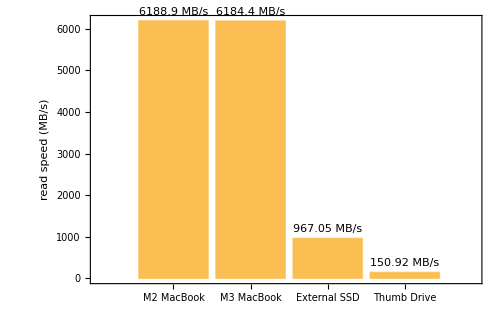

```mathematica
BarChart[
SetPrecision[readSpeeds,5],
ChartLabels->Keys@experiments,
TargetUnits->"Megabytes"/"Seconds",
Frame->True,
FrameLabel->"read speed (MB/s)",
LabelingFunction->(Placed[Row[{#," MB/s"}],Above]&),
PlotRangePadding->{Automatic,{None,Scaled[.1]}}
]
```

## Figure 2

```mathematica
plotExperiments=Catenate@experiments;
```

```mathematica
plotExperiments=Select[Catenate@experiments,!StringMatchQ[#"test_case",DigitCharacter..]&];
```

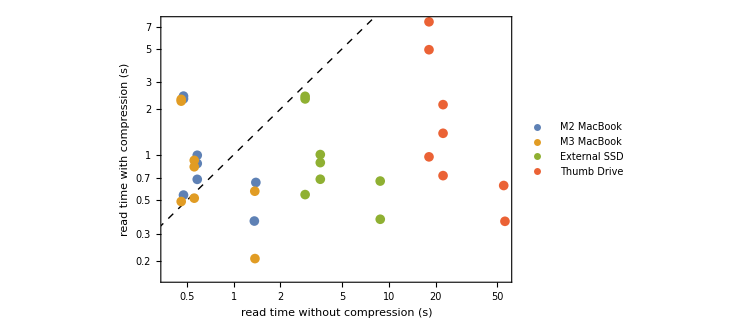

```mathematica
ListLogLogPlot[
GroupBy[
Normal@Merge[{
GroupBy[Select[plotExperiments,#algorithm==="none"&],({#platform,#"test_case"}&)->(#duration&),First],
GroupBy[Select[plotExperiments,#algorithm=!="none"&],({#platform,#"test_case"}&)->(#duration&)]
},Thread],
(#[[1,1]]&)->(#[[2]]&),
Catenate
],
Frame->True,
FrameLabel->{"read time without compression (s)","read time with compression (s)"},
Epilog->{Dashed,InfiniteLine[{0,0},{1,1}]},
PlotRange->All,
PlotLegends->Placed[Automatic,{Left,Top}]
]
```

## Figure 3

## Misc

```mathematica
ListPlot[Callout[{#"compression_ratio",#"duration"},#"test_case"]&/@experiments["M2 MacBook"]]
```

-Graphics-

```mathematica
ListPlot[Callout[{#"compression_ratio",#"duration"},#"test_case"]&/@Select[experiments["M2 MacBook"],#"test_case"==="wikipedia_small"&]]
```

-Graphics-

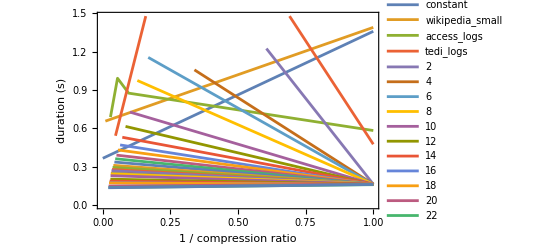

```mathematica
ListLinePlot[
GroupBy[
experiments["M2 MacBook"],
(#"test_case"&)->({#"compression_ratio",#"duration"}&)
],
Frame->True,
FrameLabel->{"1 / compression ratio","duration (s)"}
]
```

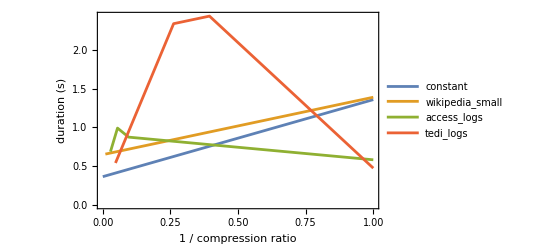

```mathematica
ListLinePlot[
GroupBy[
Select[experiments["M2 MacBook"],!StringMatchQ[#"test_case",DigitCharacter..]&],
(#"test_case"&)->({#"compression_ratio",#"duration"}&)
],
Frame->True,
FrameLabel->{"1 / compression ratio","duration (s)"}
]
```

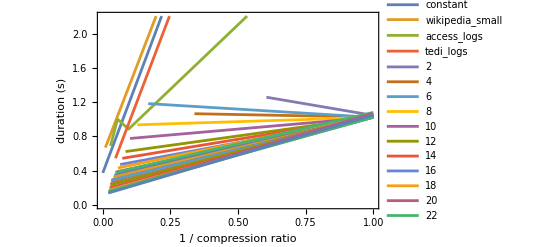

```mathematica
ListLinePlot[
GroupBy[
experiments["External SSD"],
(#"test_case"&)->({#"compression_ratio",#"duration"}&)
],
Frame->True,
FrameLabel->{"1 / compression ratio","duration (s)"}
]
```

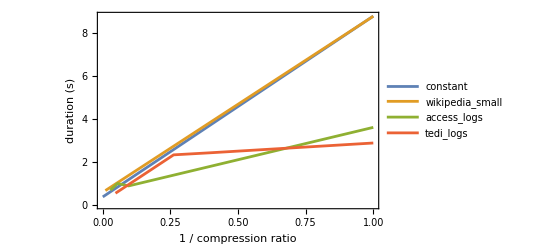

```mathematica
ListLinePlot[
GroupBy[
Select[experiments["External SSD"],!StringMatchQ[#"test_case",DigitCharacter..]&],
(#"test_case"&)->({#"compression_ratio",#"duration"}&)
],
Frame->True,
FrameLabel->{"1 / compression ratio","duration (s)"}
]
```

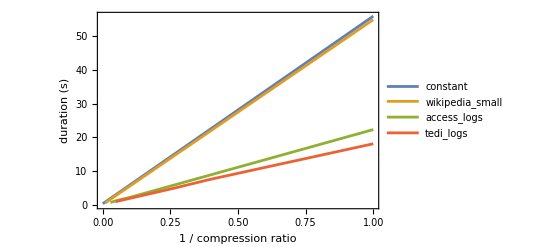

```mathematica
ListLinePlot[
GroupBy[
Select[experiments["Thumb Drive"],!StringMatchQ[#"test_case",DigitCharacter..]&],
(#"test_case"&)->({#"compression_ratio",#"duration"}&)
],
Frame->True,
FrameLabel->{"1 / compression ratio","duration (s)"}
]
```

```mathematica
ListPlot[
{
Callout[{1/#"compression_ratio",#"decompression_speed"},{#"test_case",#"algorithm"}]&/@experiments["M2 MacBook"],
Callout[{1/#"compression_ratio",#"decompression_speed"},{#"test_case",#"algorithm"}]&/@experiments["External SSD"]
},
PlotStyle->Opacity[0.5]
]
```

-Graphics-

```mathematica
ListPlot[
Map[
Callout[{1/#"compression_ratio",#"decompression_speed"},{#"test_case",#"algorithm"}]&,
experiments,
{2}
],
PlotStyle->Opacity[0.5]
]
```

-Graphics-